```mathematica
Quit[]
```

```mathematica
SetDirectory["~/Documents/Univ/SLattice/math"];
```

## Noise coeff.

```mathematica
Lsize=16;
dim=2;
```

```mathematica
xvol=Lsize^dim
```

256

```mathematica
xivec[xnum_]={Mod[xnum,Lsize,1],Quotient[xnum,Lsize,1]+1};
```

```mathematica
LengthMatrix=Table[Norm[xivec[i]-xivec[j]],{i,xvol},{j,xvol}];
```

```mathematica
CC[ks_]=Map[If[#==0,1,Sin[ks #]/(ks #)]&,LengthMatrix,{2}];
```

```mathematica
2-Log10[1/(100Lsize)]//N
```

5.20412

```mathematica
QList=ParallelTable[kks=10^logks;
Cs=N[CC[kks],{∞,16}];
Es=N[Eigensystem[Cs],{∞,16}];
Λ=DiagonalMatrix[Es[[1]]];
PP=Transpose[Es[[2]]];
QQ=Round[PP.Sqrt[Λ],10^-16];
{kks,QQ//N},{logks,Log10[1/(100Lsize)],2,10^-2}];//AbsoluteTiming
```

{2846.86,Null}

```mathematica
Select[Flatten[CC[1/(100Lsize)]-QList[[1,2]].Transpose[QList[[1,2]]]],#>10^-15&]
```

{}

```mathematica
Do[Export["QList_cite16_dim2/QList_"<>ToString[i]<>".dat",QList[[i,2]]],{i,Length[QList]}];
```

```mathematica
QList=Table[Import["QList_cite16_dim2/QList_"<>ToString[i]<>".dat"],{i,(2-Log10[1/(100Lsize)])/10^-2}]
```

```mathematica
Qint[ks_]=Interpolation[QList,InterpolationOrder->0][ks];
```

## Fourier 3-dim.

```mathematica
Lsize=4;
dim=2;
```

```mathematica
xvol=Lsize^dim
```

16

```mathematica
xList=Flatten[Table[{i-(Lsize+1)/2,j-(Lsize+1)/2,0},{i,Lsize},{j,Lsize}],1];
Length[xList]
```

16

```mathematica
LengthMatrix=Table[Norm[xList[[i]]-xList[[j]]],{i,xvol},{j,xvol}];
```

```mathematica
CC[ks_]=Map[If[#==0,1,Sin[ks #]/(ks #)]&,LengthMatrix,{2}];
```

```mathematica
kmax=2π 3;
kmin=(2π)/(3Lsize);
```

```mathematica
Nθ=Ceiling[π Lsize/(2π) kmax]
Δθ=π/Nθ;
θi[i_]=(i-1/2)Δθ;
```

38

```mathematica
Nϕ[θ_]=Ceiling[2π Sin[θ] Lsize/(2π) kmax];
Δϕ[θ_]=(2π)/Nϕ[θ];
ϕi[i_,θ_]=(i-1/2)Δϕ[θ];
```

```mathematica
ΩList=Flatten[Table[{θi[i],ϕi[j,θi[i]]}//N,{i,Nθ},{j,Nϕ[θi[i]]}],1];
Ωvol=Length[ΩList]
```

1844

```mathematica
Ωvec=Table[{Sin[ΩList[[Ωnum,1]]]Cos[ΩList[[Ωnum,2]]],Sin[ΩList[[Ωnum,1]]]Sin[ΩList[[Ωnum,2]]],Cos[ΩList[[Ωnum,1]]]},{Ωnum,Ωvol}];
```

```mathematica
jxΩ[ks_]=Table[1/(2Sqrt[π])(Cos[ks Ωvec[[Ωnum]].xList[[xnum]]]-Sin[ks Ωvec[[Ωnum]].xList[[xnum]]])Sqrt[Sin[ΩList[[Ωnum,1]]]Δθ Δϕ[ΩList[[Ωnum,1]]]],{xnum,xvol},{Ωnum,Ωvol}];//AbsoluteTiming
```

{0.910447,Null}

### test

```mathematica
XList=Table[Subscript[XX, i],{i,xvol}];
XListN[NN_]=Table[Subscript[XX, i][NN],{i,xvol}];
dXList[NN_]=Table[ⅆSubscript[XX, i][NN],{i,xvol}];
WList=Table[Subscript[WW, i],{i,Ωvol}];
dWList[NN_]=Table[ⅆSubscript[WW, i][NN],{i,Ωvol}];
```

```mathematica
NoiseTerm[ks_,NN_]=jxΩ[ks].dWList[NN];//AbsoluteTiming
```

{1.04371,Null}

```mathematica
SDEnoise[ks_]=MapThread[#1==#2&,{dXList[NN],NoiseTerm[ks,NN]}];//AbsoluteTiming
```

{0.772975,Null}

```mathematica
kks=1;
ProcNoise=ItoProcess[SDEnoise[kks],XListN[NN],{XList,Table[0,{i,xvol}]},NN,Table[WList[[i]]\[Distributed]WienerProcess[],{i,Ωvol}]];//AbsoluteTiming
```

$Aborted

```mathematica
Nsample=1000;
sol=RandomFunction[ProcNoise,{0,1,1},Nsample];
```

Function::flpar: Parameter specification {NN,XX_1,XX_2,XX_3,XX_4,XX_5,XX_6,XX_7,XX_8,XX_9,«7»} in Function[{NN,XX_1,XX_2,XX_3,XX_4,XX_5,XX_6,XX_7,XX_8,XX_9,«7»},{XX_1,XX_2,XX_3,XX_4,XX_5,XX_6,XX_7,XX_8,XX_9,XX_10,«6»}] should be a symbol or a list of symbols.

```mathematica
Length[sol["LastValues"][[1]]]
```

16

```mathematica
Cmock=Table[Correlation[Transpose[sol["LastValues"]][[i]],Transpose[sol["LastValues"]][[j]]],{i,xvol},{j,i}];//AbsoluteTiming
```

{0.019185,Null}

```mathematica
Cks=CC[kks]//N;
```

```mathematica
Sum[(Cmock[[i,j]]-Cks[[i,j]])^2,{i,xvol},{j,i}]/Sum[Cks[[i,j]]^2,{i,xvol},{j,i}]
```

0.00785635

```mathematica
Sum[(Random[Real,{-1,1}]-Cks[[i,j]])^2,{i,xvol},{j,i}]/Sum[Cks[[i,j]]^2,{i,xvol},{j,i}]
```

3.922

## Fourier 2-dim. (wrong)

```mathematica
Lsize=16;
dim=2;
```

```mathematica
xvol=Lsize^dim
```

256

```mathematica
xList=Flatten[Table[{i-(Lsize+1)/2,j-(Lsize+1)/2},{i,Lsize},{j,Lsize}],1];
Length[xList]
```

256

```mathematica
LengthMatrix=Table[Norm[xList[[i]]-xList[[j]]],{i,xvol},{j,xvol}];
```

```mathematica
CC[ks_]=Map[If[#==0,1,Sin[ks #]/(ks #)]&,LengthMatrix,{2}];
```

```mathematica
kmax=2π 10^2;
kmin=(2π)/(10^2 Lsize);
```

```mathematica
Nθ=Ceiling[π (*kmax*) Lsize]
Δθ=π/Nθ;
θi[i_]=(i-1/2)Δθ;
```

51

```mathematica
ΩList=Join[Table[{θi[i]//N,0},{i,Nθ}],Table[{θi[i]//N,π},{i,Nθ}]];
Ωvol=Length[ΩList]
```

102

```mathematica
Ωvec=Table[{Sin[ΩList[[Ωnum,1]]]Cos[ΩList[[Ωnum,2]]],Cos[ΩList[[Ωnum,1]]]},{Ωnum,Ωvol}];
```

```mathematica
jxΩ[ks_]=Table[1/(2Sqrt[2])(Cos[ks Ωvec[[Ωnum]].xList[[xnum]]]-Sin[ks Ωvec[[Ωnum]].xList[[xnum]]])Sqrt[Sin[ΩList[[Ωnum,1]]]Δθ],{xnum,xvol},{Ωnum,Ωvol}];//AbsoluteTiming
```

{0.293769,Null}

### test

```mathematica
XList=Table[Subscript[XX, i],{i,xvol}];
XListN[NN_]=Table[Subscript[XX, i][NN],{i,xvol}];
dXList[NN_]=Table[ⅆSubscript[XX, i][NN],{i,xvol}];
WList=Table[Subscript[WW, i],{i,Ωvol}];
dWList[NN_]=Table[ⅆSubscript[WW, i][NN],{i,Ωvol}];
```

```mathematica
NoiseTerm[ks_,NN_]=jxΩ[ks].dWList[NN];//AbsoluteTiming
```

{0.135508,Null}

```mathematica
SDEnoise[ks_]=MapThread[#1==#2&,{dXList[NN],NoiseTerm[ks,NN]}];//AbsoluteTiming
```

{0.098031,Null}

```mathematica
kks=1;
ProcNoise=ItoProcess[SDEnoise[kks],XListN[NN],{XList,Table[0,{i,xvol}]},NN,Table[WList[[i]]\[Distributed]WienerProcess[],{i,Ωvol}]];//AbsoluteTiming
```

{2.90844,Null}

```mathematica
Nsample=1000;
sol=RandomFunction[ProcNoise,{0,1,1},Nsample];
```

Function::flpar: Parameter specification {NN,XX_1,XX_2,XX_3,XX_4,XX_5,XX_6,XX_7,XX_8,XX_9,«247»} in Function[{NN,XX_1,XX_2,XX_3,XX_4,XX_5,XX_6,XX_7,XX_8,XX_9,«247»},{XX_1,XX_2,XX_3,XX_4,XX_5,XX_6,XX_7,XX_8,XX_9,XX_10,«246»}] should be a symbol or a list of symbols.

```mathematica
Length[sol["LastValues"][[1]]]
```

256

```mathematica
Cmock=Table[Correlation[Transpose[sol["LastValues"]][[i]],Transpose[sol["LastValues"]][[j]]],{i,xvol},{j,i}];//AbsoluteTiming
```

{29.1077,Null}

```mathematica
Cks=CC[kks]//N;
```

```mathematica
Sum[(Cmock[[i,j]]-Cks[[i,j]])^2,{i,xvol},{j,i}]/Sum[Cks[[i,j]]^2,{i,xvol},{j,i}]
```

1.01439

```mathematica
Sum[(Random[Real,{-1,1}]-Cks[[i,j]])^2,{i,xvol},{j,i}]/Sum[Cks[[i,j]]^2,{i,xvol},{j,i}]
```

9.37567

## Chaotic

```mathematica
mm=10^-5;
VV[phi_]=1/2 mm^2 phi^2;
```

```mathematica
rho[phi_,pi_]=1/2 pi^2+VV[phi];
HH[phi_,pi_]=Sqrt[rho[phi,pi]];
rhodot[phi_,pi_]=3HH[phi,pi] pi^2;
```

## C++

### EM_test

```mathematica
EMtestList=Import["c++/EM_test.dat"];
```

```mathematica
sampleList=Table[{EMtestList[[j,1]],EMtestList[[j,i]]},{i,2,11},{j,Length[EMtestList]}];
```

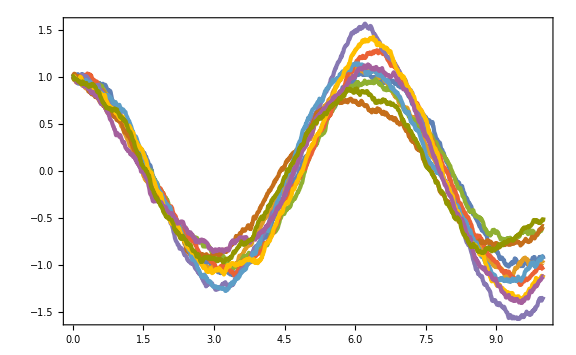

```mathematica
ListPlot[sampleList]
```

```mathematica
SDE=ItoProcess[{ⅆx[t]==p[t]ⅆt+0.1ⅆw[t],ⅆp[t]==-x[t]ⅆt},x[t],{{x,p},{1,0}},t,w\[Distributed]WienerProcess[]];
```

```mathematica
sample=RandomFunction[SDE,{0,10,0.01},10];
```

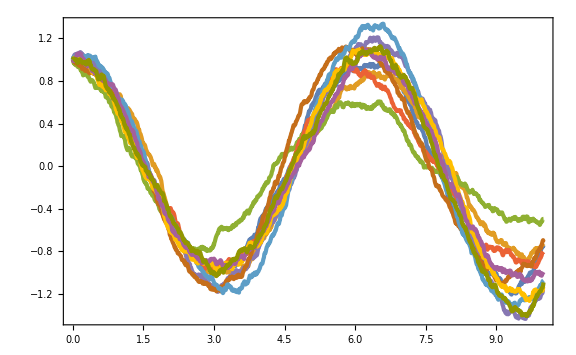

```mathematica
ListLinePlot[sample]
```

### noise_test

```mathematica
Lsize=16;
dim=2;
```

```mathematica
xvol=Lsize^dim
```

256

```mathematica
xList=Flatten[Table[{i-(Lsize+1)/2,j-(Lsize+1)/2,0},{i,Lsize},{j,Lsize}],1];
Length[xList]
```

256

```mathematica
LengthMatrix=Table[Norm[xList[[i]]-xList[[j]]],{i,xvol},{j,xvol}];
```

```mathematica
CC[ks_]=Map[If[#==0,1,Sin[ks #]/(ks #)]&,LengthMatrix,{2}];
```

```mathematica
kmax=3 2π;
kmin=(2π)/(3Lsize);
```

```mathematica
kks=kmax;
```

```mathematica
Nθ=Ceiling[π kks/kmin]
Δθ=π/Nθ;
θi[i_]=(i-1/2)Δθ;
```

453

```mathematica
Nϕ[θ_]=Ceiling[2π Sin[θ] kks/kmin];
Δϕ[θ_]=(2π)/Nϕ[θ];
ϕi[i_,θ_]=(i-1/2)Δϕ[θ];
```

```mathematica
ΩList=Flatten[Table[{θi[i],ϕi[j,θi[i]]}//N,{i,Nθ},{j,Nϕ[θi[i]]}],1];
Ωvol=Length[ΩList]
```

261157

```mathematica
Ωvec=Table[{Sin[ΩList[[Ωnum,1]]]Cos[ΩList[[Ωnum,2]]],Sin[ΩList[[Ωnum,1]]]Sin[ΩList[[Ωnum,2]]],Cos[ΩList[[Ωnum,1]]]},{Ωnum,Ωvol}];
jxΩ=Table[1/(2Sqrt[π])(Cos[kks Ωvec[[Ωnum]].xList[[xnum]]]-Sin[kks Ωvec[[Ωnum]].xList[[xnum]]])Sqrt[Sin[ΩList[[Ωnum,1]]]Δθ Δϕ[ΩList[[Ωnum,1]]]],{xnum,xvol},{Ωnum,Ωvol}];//AbsoluteTiming
```

{2.58936,Null}

```mathematica
Ωvec[[1]].xList[[1]]
```

-0.0292286

```mathematica
CC[kks]//N
```

{{1.,0.,0.,0.,0.,0.0374731,-0.022912,0.00138634,0.,-0.022912,0.00173214,-0.0134423,0.,0.00138634,-0.0134423,-0.0123843},{0.,1.,0.,0.,0.0374731,0.,0.0374731,-0.022912,-0.022912,0.,-0.022912,0.00173214,0.00138634,0.,0.00138634,-0.0134423},{0.,0.,1.,0.,-0.022912,0.0374731,0.,0.0374731,0.00173214,-0.022912,0.,-0.022912,-0.0134423,0.00138634,0.,0.00138634},{0.,0.,0.,1.,0.00138634,-0.022912,0.0374731,0.,-0.0134423,0.00173214,-0.022912,0.,-0.0123843,-0.0134423,0.00138634,0.},{0.,0.0374731,-0.022912,0.00138634,1.,0.,0.,0.,0.,0.0374731,-0.022912,0.00138634,0.,-0.022912,0.00173214,-0.0134423},{0.0374731,0.,0.0374731,-0.022912,0.,1.,0.,0.,0.0374731,0.,0.0374731,-0.022912,-0.022912,0.,-0.022912,0.00173214},{-0.022912,0.0374731,0.,0.0374731,0.,0.,1.,0.,-0.022912,0.0374731,0.,0.0374731,0.00173214,-0.022912,0.,-0.022912},{0.00138634,-0.022912,0.0374731,0.,0.,0.,0.,1.,0.00138634,-0.022912,0.0374731,0.,-0.0134423,0.00173214,-0.022912,0.},{0.,-0.022912,0.00173214,-0.0134423,0.,0.0374731,-0.022912,0.00138634,1.,0.,0.,0.,0.,0.0374731,-0.022912,0.00138634},{-0.022912,0.,-0.022912,0.00173214,0.0374731,0.,0.0374731,-0.022912,0.,1.,0.,0.,0.0374731,0.,0.0374731,-0.022912},{0.00173214,-0.022912,0.,-0.022912,-0.022912,0.0374731,0.,0.0374731,0.,0.,1.,0.,-0.022912,0.0374731,0.,0.0374731},{-0.0134423,0.00173214,-0.022912,0.,0.00138634,-0.022912,0.0374731,0.,0.,0.,0.,1.,0.00138634,-0.022912,0.0374731,0.},{0.,0.00138634,-0.0134423,-0.0123843,0.,-0.022912,0.00173214,-0.0134423,0.,0.0374731,-0.022912,0.00138634,1.,0.,0.,0.},{0.00138634,0.,0.00138634,-0.0134423,-0.022912,0.,-0.022912,0.00173214,0.0374731,0.,0.0374731,-0.022912,0.,1.,0.,0.},{-0.0134423,0.00138634,0.,0.00138634,0.00173214,-0.022912,0.,-0.022912,-0.022912,0.0374731,0.,0.0374731,0.,0.,1.,0.},{-0.0123843,-0.0134423,0.00138634,0.,-0.0134423,0.00173214,-0.022912,0.,0.00138634,-0.022912,0.0374731,0.,0.,0.,0.,1.}}

```mathematica
Sqrt[0.05^2 xvol^2/xvol]
```

0.2

### chaotic

```mathematica
QList=Import["c++/chaotic/chaotic_Q.dat"];
PList=Import["c++/chaotic/chaotic_P.dat"];
HList=Import["c++/chaotic/chaotic_H.dat"];
zList=Import["c++/chaotic/chaotic_zeta.dat"];
LatticeList=Import["c++/chaotic/chaotic_Lattice.dat"];
```

```mathematica
xvol=Length[LatticeList]
```

289

```mathematica
Q1List=Table[{QList[[i,1]],QList[[i,2]]},{i,Length[QList]}];
P1List=Table[{PList[[i,1]],PList[[i,2]]},{i,Length[PList]}];
H1List=Table[{HList[[i,1]],HList[[i,2]]},{i,Length[HList]}];
HcList=Table[{HList[[i,1]],HList[[i,1+(xvol+1)/2]]},{i,Length[HList]}];
```

```mathematica
Lsize=16+1;
kmax=3 2π;
kmin=(2π)/(3Lsize);
```

```mathematica
mm=10^-2;
V[Q_]=1/2 mm^2 Q^2;
H[Q_,P_]=Sqrt[(P^2/2+V[Q])/3];
```

```mathematica
tf=Log[kmax/kmin];tf//N
```

5.03044

```mathematica
sol=NDSolve[{Q'[t]==P[t]/H[Q[t],P[t]],P'[t]==-3P[t]-V'[Q[t]]/H[Q[t],P[t]],Q[0]==15,P[0]==(-V'[Q[0]])/Sqrt[3V[Q[0]]]},{Q[t],P[t]},{t,0,tf}];
```

```mathematica
Qsol[t_]=Q[t]/.sol;
Psol[t_]=P[t]/.sol;
Hsol[t_]=H[Qsol[t],Psol[t]];
```

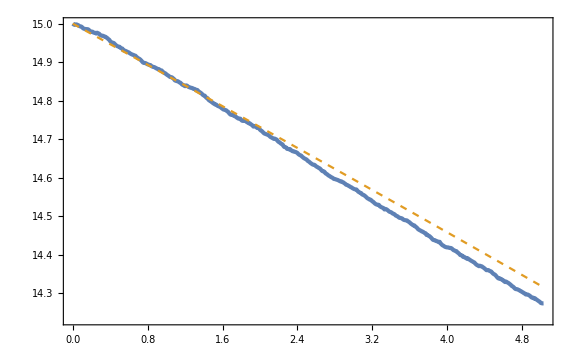

```mathematica
Show[ListPlot[Q1List],Plot[Qsol[t],{t,0,tf},PlotStyle->{Color[2],Dashed}]]
```

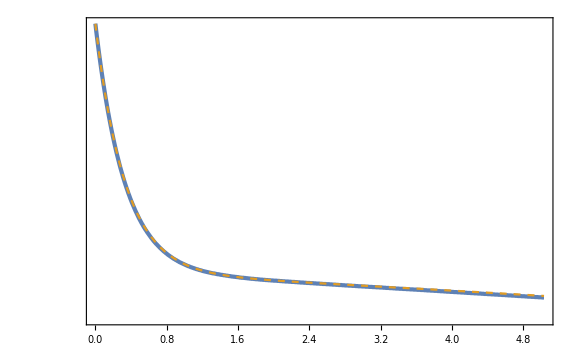

```mathematica
Show[ListLogPlot[Abs[P1List]],LogPlot[-Psol[t],{t,0,tf},PlotStyle->{Color[2],Dashed},PlotRange->Full]]
```

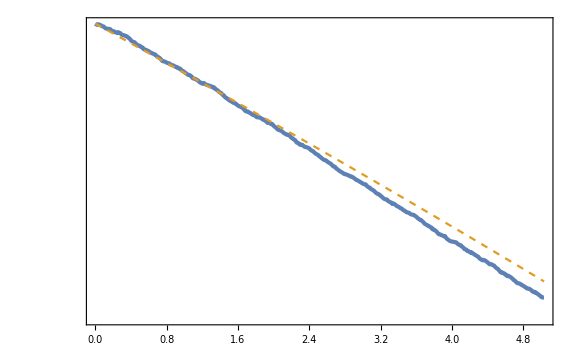

```mathematica
Show[ListLogPlot[H1List],LogPlot[Hsol[t],{t,0,tf},PlotStyle->{Color[2],Dashed}]]
```

```mathematica
Length[QList]
```

504

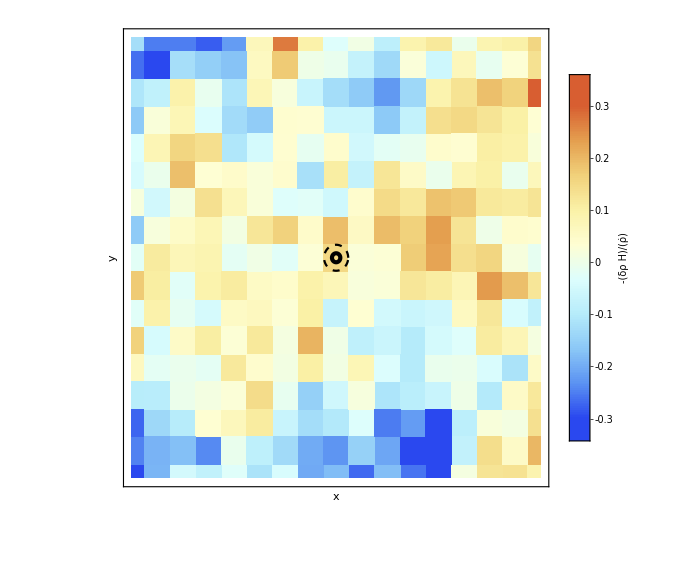

```mathematica
is=400;
(*QLattice=Table[{LatticeList[[cite,1]],LatticeList[[cite,2]],QList[[is,cite+1]]},{cite,Length[LatticeList]}];*)
zLattice=Table[{LatticeList[[cite,1]],LatticeList[[cite,2]],zList[[is,cite+1]]},{cite,Length[LatticeList]}];
(*Show[ListDensityPlot[QLattice,InterpolationOrder->0,PlotLegends->BarLegend[Automatic,LegendLabel->ϕ],FrameTicks->None,FrameLabel->{{y,None},{x,N==HcList[[is,1]]}}],ParametricPlot[{HcList[[1,2]]/(Exp[HcList[[is,1]]]HcList[[is,2]])Lsize/2{Cos[θ],Sin[θ]},(2π)/(kmin Exp[HcList[[is,1]]]2){Cos[θ],Sin[θ]}},{θ,0,2π},PlotStyle->{{Black,AbsoluteThickness[3]},{Black,Dashed}}]]*)
Show[ListDensityPlot[zLattice,InterpolationOrder->0,PlotLegends->BarLegend[Automatic,LegendLabel->-"H" δρ/ρ̇],FrameTicks->None,FrameLabel->{{y,None},{x,N==HcList[[is,1]]}},ColorFunction->(ColorData["LightTemperatureMap"][(#1/0.3+1)/2]&),ColorFunctionScaling->False],ParametricPlot[{HcList[[1,2]]/(Exp[HcList[[is,1]]]HcList[[is,2]])Lsize/2{Cos[θ],Sin[θ]},(2π)/(kmin Exp[HcList[[is,1]]]2){Cos[θ],Sin[θ]}},{θ,0,2π},PlotStyle->{{Black,AbsoluteThickness[3]},{Black,Dashed}}]]
```

```mathematica
zplotList=Table[Show[ListDensityPlot[Table[{LatticeList[[cite,1]],LatticeList[[cite,2]],zList[[i,cite+1]]},{cite,Length[LatticeList]}],InterpolationOrder->0,PlotLegends->BarLegend[{Automatic,{-0.3,0.3}},LegendLabel->-"H" δρ/ρ̇],FrameTicks->None,FrameLabel->{{y,None},{x,N==HcList[[i,1]]}},ColorFunction->(ColorData["LightTemperatureMap"][(#1/0.3+1)/2]&),ColorFunctionScaling->False],ParametricPlot[{HcList[[1,2]]/(Exp[HcList[[i,1]]]HcList[[i,2]])Lsize/2{Cos[θ],Sin[θ]},(2π)/(kmin Exp[HcList[[i,1]]]2){Cos[θ],Sin[θ]}},{θ,0,2π},PlotStyle->{{Black,AbsoluteThickness[3]},{Black,Dashed}}]],{i,1,Length[zList],10}];
```

```mathematica
Export["c++/chaotic/chaotic_zeta.gif",zplotList];
```